```mathematica
L[μ_]:=(b+μ*s)^n*Exp[-(b+μ*s)]
L[μ]
L[0]
q0[μ_]:=FullSimplify[-2*PowerExpand@Log[L[0]/L[μ]]]
q0[μ]
a0[μ_]:=FullSimplify[q0[μ]/.{n->b+μ*s}]
a0[μ]
```

ⅇ^(-b-s μ) (b+s μ)^n

b^n ⅇ^-b

-2 (s μ+n Log[b]-n Log[b+s μ])

-2 (s μ+(b+s μ) (Log[b]-Log[b+s μ]))

```mathematica
Nb=100
t[μ_]:=FullSimplify[a0[μ]/.{b->Nb,s->1}]
t[μ]
```

100

-2 μ+2 (100+μ) Log[1+μ/100]

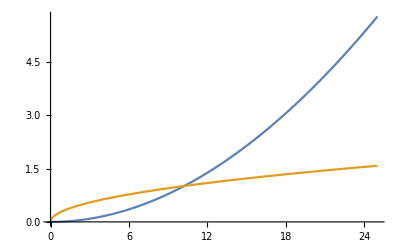

```mathematica
g[μ_]:=Sqrt[μ/Sqrt[Nb]]
Plot[{t[μ],g[μ]},{μ,0,25}]
```

```mathematica
FindRoot[t[μ]-1,{μ,0,25}]
```

{μ→10.1653}

```mathematica
N[t[10]]
N[t[10.165313537186384]]
```

0.96824

1.